## Steps

Separate the points into x -axis (plane mirror points) and unknown reflecting curve incident points based on y coordinates

curvepts = {{-6.86151,4.52874},{-1.05854,5.96498},{5.16601,5.16601},{6.74625,4.57775}}

xaxispts = {{-4.35714,0},{0,0},{3.35734,0},{6.00383,0}}

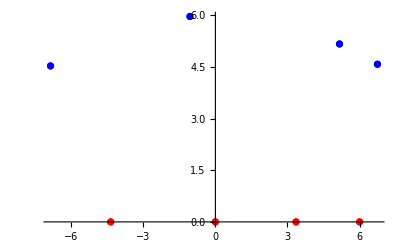

```mathematica
For[xaxispts = {}; i=0, i<Length[intersecpts], i++; If[intersecpts[[i, 2]]==0, AppendTo[xaxispts, intersecpts[[i]]]]]
curvepts = Sort[DeleteCases[intersecpts, Alternatives @@ xaxispts]];
xaxispts = Sort[xaxispts];
Print["curvepts = ", curvepts]
Print["xaxispts = ", xaxispts]
intersecplot2 = ListPlot[{#} & /@ intersecpts, PlotRange->Full,PlotStyle->{Blue, Red, Blue, Red, Blue, Red, Blue, Red}]
```

```mathematica
For[eqndataset = {}; z=0, z<Length[xaxispts], z++;
	For[pteqnmatrix = ConstantArray[0, {Length[curvepts]+1, Length[xaxispts]}]; i=0, i<Length[curvepts], i++;
		pteqnmatrix = ReplacePart[pteqnmatrix, 
		{1, i}->Last[List @@ Reduce[y-InterpolatingPolynomial[{xaxispts[[z]], curvepts[[i]]},x]==0,y]]];
		For[j=0, j<Length[xaxispts], j++; If[j==z, Continue[]];  
			pteqnmatrix = ReplacePart[pteqnmatrix, 
			{j+1, i}->{Last[List @@ Reduce[y - InterpolatingPolynomial[{curvepts[[i]], xaxispts[[j]]},x]==0,y]],
			Last[List @@ Reduce[y-0==-Coefficient[Last[List @@ Reduce[y - InterpolatingPolynomial[{curvepts[[i]], xaxispts[[j]]},x]==0,y]],x](x-xaxispts[[j]][[1]]),y]]}
		(* Reflection from the plane mirror added here simulatenously in set (left is incident, right is reflected *)
			]]];
	AppendTo[eqndataset, pteqnmatrix]]
eqndataset
eqndatasetcopy = eqndataset;
```

{{{-7.87917-1.80834 x,7.87917+1.80834 x,2.36361+0.542469 x,1.79638+0.412284 x},{0,0,0,0},{{0.-0.660021 x,0.+0.660021 x},{0.-5.63513 x,0.+5.63513 x},{0.+1. x,0.-1. x},{0.+0.678563 x,0.-0.678563 x}},{{1.48789-0.443175 x,-1.48789+0.443175 x},{4.53511-1.3508 x,-4.53511+1.3508 x},{-9.58939+2.85625 x,9.58939-2.85625 x},{-4.53511+1.3508 x,4.53511-1.3508 x}},{{2.11341-0.352011 x,-2.11341+0.352011 x},{5.07093-0.844615 x,-5.07093+0.844615 x},{37.0197-6.16601 x,-37.0197+6.16601 x},{-37.0197+6.16601 x,37.0197-6.16601 x}}},{{0.-0.660021 x,0.-5.63513 x,0.+1. x,0.+0.678563 x},{{-7.87917-1.80834 x,7.87917+1.80834 x},{7.87917+1.80834 x,-7.87917-1.80834 x},{2.36361+0.542469 x,-2.36361-0.542469 x},{1.79638+0.412284 x,-1.79638-0.412284 x}},{0,0,0,0},{{1.48789-0.443175 x,-1.48789+0.443175 x},{4.53511-1.3508 x,-4.53511+1.3508 x},{-9.58939+2.85625 x,9.58939-2.85625 x},{-4.53511+1.3508 x,4.53511-1.3508 x}},{{2.11341-0.352011 x,-2.11341+0.352011 x},{5.07093-0.844615 x,-5.07093+0.844615 x},{37.0197-6.16601 x,-37.0197+6.16601 x},{-37.0197+6.16601 x,37.0197-6.16601 x}}},{{1.48789-0.443175 x,4.53511-1.3508 x,-9.58939+2.85625 x,-4.53511+1.3508 x},{{-7.87917-1.80834 x,7.87917+1.80834 x},{7.87917+1.80834 x,-7.87917-1.80834 x},{2.36361+0.542469 x,-2.36361-0.542469 x},{1.79638+0.412284 x,-1.79638-0.412284 x}},{{0.-0.660021 x,0.+0.660021 x},{0.-5.63513 x,0.+5.63513 x},{0.+1. x,0.-1. x},{0.+0.678563 x,0.-0.678563 x}},{0,0,0,0},{{2.11341-0.352011 x,-2.11341+0.352011 x},{5.07093-0.844615 x,-5.07093+0.844615 x},{37.0197-6.16601 x,-37.0197+6.16601 x},{-37.0197+6.16601 x,37.0197-6.16601 x}}},{{2.11341-0.352011 x,5.07093-0.844615 x,37.0197-6.16601 x,-37.0197+6.16601 x},{{-7.87917-1.80834 x,7.87917+1.80834 x},{7.87917+1.80834 x,-7.87917-1.80834 x},{2.36361+0.542469 x,-2.36361-0.542469 x},{1.79638+0.412284 x,-1.79638-0.412284 x}},{{0.-0.660021 x,0.+0.660021 x},{0.-5.63513 x,0.+5.63513 x},{0.+1. x,0.-1. x},{0.+0.678563 x,0.-0.678563 x}},{{1.48789-0.443175 x,-1.48789+0.443175 x},{4.53511-1.3508 x,-4.53511+1.3508 x},{-9.58939+2.85625 x,9.58939-2.85625 x},{-4.53511+1.3508 x,4.53511-1.3508 x}},{0,0,0,0}}}

Plot of some reflections from source 1 to point 4

```mathematica
eqndataset[[1]] // MatrixForm
```

(-7.87917-1.80834 x | 7.87917+1.80834 x | 2.36361+0.542469 x | 1.79638+0.412284 x
0 | 0 | 0 | 0
{0.-0.660021 x,0.+0.660021 x} | {0.-5.63513 x,0.+5.63513 x} | {0.+1. x,0.-1. x} | {0.+0.678563 x,0.-0.678563 x}
{1.48789-0.443175 x,-1.48789+0.443175 x} | {4.53511-1.3508 x,-4.53511+1.3508 x} | {-9.58939+2.85625 x,9.58939-2.85625 x} | {-4.53511+1.3508 x,4.53511-1.3508 x}
{2.11341-0.352011 x,-2.11341+0.352011 x} | {5.07093-0.844615 x,-5.07093+0.844615 x} | {37.0197-6.16601 x,-37.0197+6.16601 x} | {-37.0197+6.16601 x,37.0197-6.16601 x})

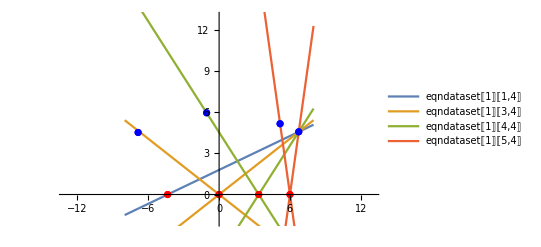

```mathematica
p1 = Plot[{eqndataset[[1]][[1,4]],eqndataset[[1]][[3,4]],eqndataset[[1]][[4,4]],eqndataset[[1]][[5,4]]}
, {x, -8, 8}, PlotLegends->"Expressions"];
Show[p1, intersecplot2, PlotRange->{{-13,13},{-2, 13}}]
```

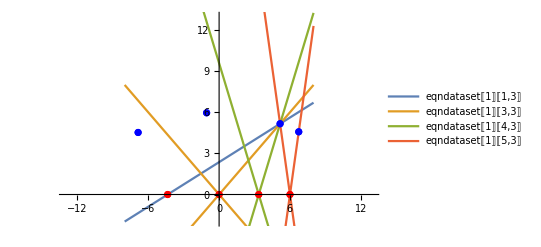

```mathematica
p1 = Plot[{eqndataset[[1]][[1,3]],eqndataset[[1]][[3,3]],eqndataset[[1]][[4,3]],eqndataset[[1]][[5,3]]}
, {x, -8, 8}, PlotLegends->"Expressions"];
Show[p1, intersecplot2, PlotRange->{{-13,13},{-2, 13}}]
```

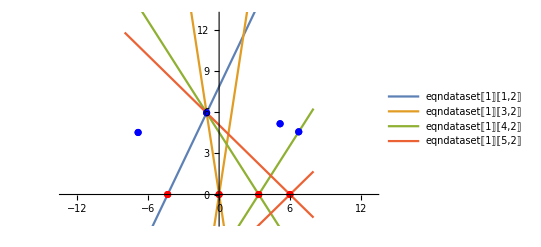

```mathematica
p1 = Plot[{eqndataset[[1]][[1,2]],eqndataset[[1]][[3,2]],eqndataset[[1]][[4,2]],eqndataset[[1]][[5,2]]}
, {x, -8, 8}, PlotLegends->"Expressions"];
Show[p1, intersecplot2, PlotRange->{{-13,13},{-2, 13}}]
```

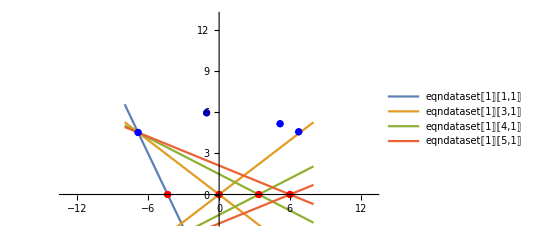

```mathematica
p1 = Plot[{eqndataset[[1]][[1,1]],eqndataset[[1]][[3,1]],eqndataset[[1]][[4,1]],eqndataset[[1]][[5,1]]}
, {x, -8, 8}, PlotLegends->"Expressions"];
Show[p1, intersecplot2, PlotRange->{{-13,13},{-2, 13}}]
```

Function for initial 3 point tuple permutations

```mathematica
pttuplefunc[domainls_, codomainls_]:=
	Module[{tupleset={}},
	For[i=0, i<Length[domainls], i++;
		For[j=0, j<Length[codomainls], j++;
			For[k=0, k<Length[domainls], k++;
				tupleset = AppendTo[tupleset, {domainls[[i]],codomainls[[j]], domainls[[k]]}];
			]]];
	Return[tupleset, Module]];
```

Path permutations till the first plane mirror reflection

```mathematica
tuple3point = pttuplefunc[xaxispts, curvepts]
Print["No of tuples = ", Length[tuple3point]]
```

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{0,0}},{{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{6.74625,4.57775},{6.00383,0}}}

No of tuples = 64

We get a total of 64 three point paths that are possible. Now after the 3 points, the next point comes through the reflection, so after reflections we can eliminate all all points in the path permutations that don’t satisfy the eqn of reflected ray

```mathematica
temp1 = reflecdrop[tuple3point]
Print["No of tuples left = ", Length[temp1]]
```

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601}}}

No of tuples left = 24

So we have 24 paths left out of 64.

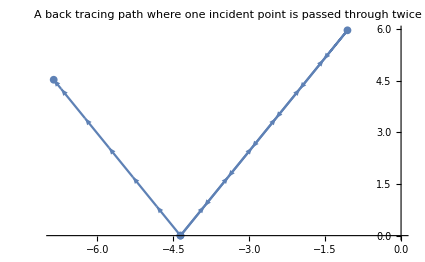

```mathematica
ListLinePlot[temp1[[2]], PlotMarkers->{Automatic, 8}, Axes->True, AxesOrigin->{0,0}, MeshFunctions -> {#2 &}, Mesh -> 6, MeshStyle -> Opacity[0], 
  MeshShading -> {Arrowheads[Small]}, DataRange -> {0, 4 Pi}, PlotLabel->"A back tracing path where one incident point is passed through twice "] /. Line -> Arrow
```

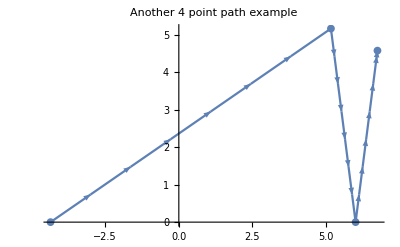

```mathematica
ListLinePlot[temp1[[4]], PlotMarkers->{Automatic, 8}, Axes->True, AxesOrigin->{0,0}, MeshFunctions -> {#2 &}, Mesh -> 6, MeshStyle -> Opacity[0], 
  MeshShading -> {Arrowheads[Small]}, DataRange -> {0, 4 Pi}, PlotLabel->"Another 4 point path example"] /. Line -> Arrow
```

```mathematica
ListLinePlot[temp1, PlotMarkers->{Automatic, 8}, Axes->True, AxesOrigin->{0,0}, PlotLabel->"Plot of all the 4 point paths"]
```

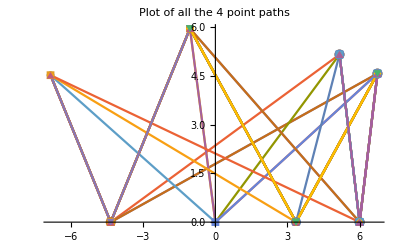

Next we again come back to the curve pts from which we again have choice of all the points in x axis as the next destination since we include back tracing

```mathematica
temp2 = path2func[temp1]
Print["No of tuples = ", Length[temp2]]
```

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}}}

No of tuples = 96

Again we got 96 new permutations of path, now next we have reflection and again we eliminate those paths which don’t satisfy our reflected ray equation

```mathematica
temp3 = reflecdrop[temp2]
Print["No of tuples left = ", Length[temp3]]
```

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775}}}

No of tuples left = 40

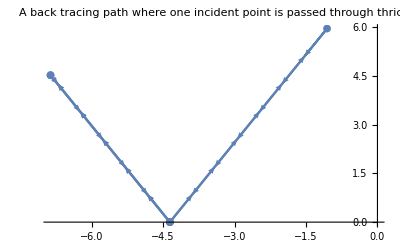

```mathematica
ListLinePlot[temp3[[1]], PlotMarkers->{Automatic, 8}, Axes->True, AxesOrigin->{0,0}, MeshFunctions -> {#2 &}, Mesh -> 6, MeshStyle -> Opacity[0], 
  MeshShading -> {Arrowheads[Small]}, DataRange -> {0, 4 Pi}, PlotLabel->"A back tracing path where one incident point is passed through thrice "] /. Line -> Arrow
```

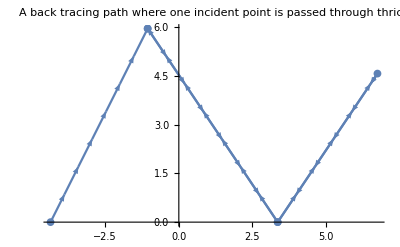

```mathematica
ListLinePlot[temp3[[4]], PlotMarkers->{Automatic, 8}, Axes->True, AxesOrigin->{0,0}, MeshFunctions -> {#2 &}, Mesh -> 6, MeshStyle -> Opacity[0], 
  MeshShading -> {Arrowheads[Small]}, DataRange -> {0, 4 Pi}, PlotLabel->"A back tracing path where one incident point is passed through thrice "] /. Line -> Arrow
```

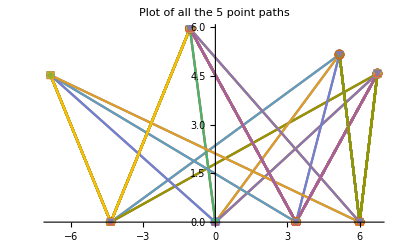

```mathematica
ListLinePlot[temp3, PlotMarkers->{Automatic, 8}, Axes->True, AxesOrigin->{0,0}, PlotLabel->"Plot of all the 5 point paths"]
```

Next we again come back to the curve pts from which we again have choice of all the points in x axis as the next destination since we include back tracing

```mathematica
temp4 = path2func[temp3]
Print["No of tuples = ", Length[temp4]]
```

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}}}

No of tuples = 160

Again we got 160 new permutations of path, now next we have reflection and again we eliminate those paths which don’t satisfy our reflected ray equation

```mathematica
temp5 = reflecdrop[temp4]
Print["No of tuples left = ", Length[temp5]]
```

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601}}}

No of tuples left = 64

```mathematica
ListLinePlot[temp5[[2]], PlotMarkers->{Automatic, 8}, Axes->True, AxesOrigin->{0,0}, MeshFunctions -> {#2 &}, Mesh -> 6, MeshStyle -> Opacity[0], 
  MeshShading -> {Arrowheads[Small]}, DataRange -> {0, 4 Pi}] /. Line -> Arrow
```

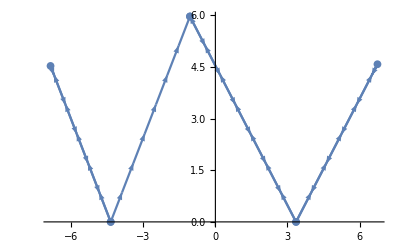

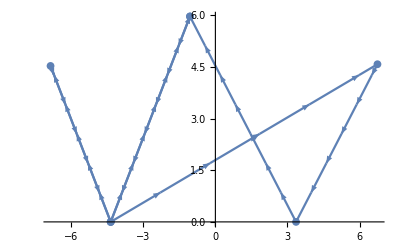

```mathematica
ListLinePlot[temp5[[12]], PlotMarkers->{Automatic, 8}, Axes->True, AxesOrigin->{0,0}, MeshFunctions -> {#2 &}, Mesh -> 6, MeshStyle -> Opacity[0], 
  MeshShading -> {Arrowheads[Small]}, DataRange -> {0, 4 Pi}] /. Line -> Arrow
```

We remove all the paths which don’t have all the points given in the input atleast once

{{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}}}

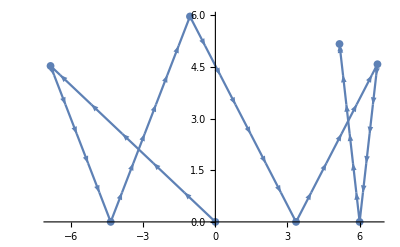

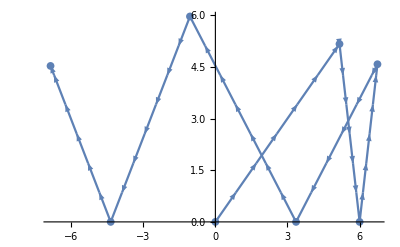

```mathematica
a = temp5;
For[new={}; i=0, i<Length[a], i++;
	If[CountDistinct[a[[i]]]==Length[intersecpts], new = AppendTo[new, a[[i]]]]]
new
ListLinePlot[new[[1]], PlotMarkers->{Automatic, 8}, Axes->True, AxesOrigin->{0,0}, MeshFunctions -> {#2 &}, Mesh -> 6, MeshStyle -> Opacity[0], 
  MeshShading -> {Arrowheads[Small]}, DataRange -> {0, 4 Pi}] /. Line -> Arrow
ListLinePlot[new[[2]], PlotMarkers->{Automatic, 8}, Axes->True, AxesOrigin->{0,0}, MeshFunctions -> {#2 &}, Mesh -> 6, MeshStyle -> Opacity[0], 
  MeshShading -> {Arrowheads[Small]}, DataRange -> {0, 4 Pi}] /. Line -> Arrow
```